# Dynamics of Interacting Radiation, Pressure-less Dark Matter and Dark Energy with a Non-Linear Quadratic EoS

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*System of dimensionless differential equations*)
(*Dark energy, x, Hubble expansion, y, dark matter, z, and  radiation, r*)
de1:=x'=-3*y*q1^2*(x-ℛ)*(1-x)*r*z
de2:=y'=-y^2-(1/6)*(z+2*r-2x)
de3:=z'=-3*y*z*(1-q2^2*r*(x-ℛ)*(1-x))
de4:=r'=-3*y*r*(4/3+(-q1^2+q2^2)*z*(x-ℛ)*(1-x))
```

```mathematica
FPs=Solve[{de2==0,de3==0,de4==0},{x,y,z,r}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0,r→1/2 (2 x-z)},{y→-(√(3 q2^2 x-(2 q1^2)/((q1^2-q2^2) (1-x) (x-ℛ))-q2^2/((q1^2-q2^2) (1-x) (x-ℛ))))/(3 q2),z→-(-(4 q1^2)/((q1^2-q2^2) (1-x) (x-ℛ))+(4 q2^2)/((q1^2-q2^2) (1-x) (x-ℛ)))/(3 q2^2),r→1/((q1^2-q2^2) (1-x) (x-ℛ))},{y→(√(3 q2^2 x-(2 q1^2)/((q1^2-q2^2) (1-x) (x-ℛ))-q2^2/((q1^2-q2^2) (1-x) (x-ℛ))))/(3 q2),z→-(-(4 q1^2)/((q1^2-q2^2) (1-x) (x-ℛ))+(4 q2^2)/((q1^2-q2^2) (1-x) (x-ℛ)))/(3 q2^2),r→1/((q1^2-q2^2) (1-x) (x-ℛ))},{x→3 y^2,z→0,r→0}}

```mathematica
(*System of dimensionless differential equations*)
(*Dark energy, x, Hubble expansion, y, dark matter, z*)
de1:=x'=-3*y*q1*(x-ℛ)*(1-x)*z
de2:=y'=-y^2-(1/6)*(z-2x)
de3:=z'=-3*y*z*(1+(-q1)*(x-ℛ)*(1-x))
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0},{x,y}]
```

{{x→z/2,y→0},{x→1,y→-(√(2-z))/(√6)},{x→1,y→(√(2-z))/(√6)},{x→ℛ,y→-(√(-z+2 ℛ))/(√6)},{x→ℛ,y→(√(-z+2 ℛ))/(√6)}}

```mathematica
FP[1]={x/.FPs[[1,1]],y/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y/.FPs[[2,2]]};
FP[3]={x/.FPs[[3,1]],y/.FPs[[3,2]]};
FP[4]={x/.FPs[[4,1]],y/.FPs[[4,2]]};
FP[5]={x/.FPs[[5,1]],y/.FPs[[5,2]]};
```

```mathematica
Eq1[q1_,ℛ_]=de1
Eq2[ℛ_]=de2
Eq3[q1_,ℛ_]=de3
```

-3 q1 (1-x) y z (x-ℛ)

-y^2+1/6 (2 x-z)

-3 y z (1-q1 (1-x) (x-ℛ))

```mathematica
Manipulate[StreamPlot3D[{Eq1[q1,ℛ],Eq2[ℛ],Eq3[q1,ℛ]},{x,0,1},{y,-1,1},{z,0,10},AxesLabel->{"x","y","z"}],{q1,0,10,Appearance->"Open"},{ℛ,0,1,Appearance->"Open"}]
```

```mathematica
xPart=Simplify[Integrate[(1/(q1*(x-ℛ)*(1-x)))+q2/q1,x,Assumptions->{0<ℛ<1,x<1}]]
```

(q2 x (-1+ℛ)+Log[-1+x]-Log[x-ℛ])/(q1 (-1+ℛ))

```mathematica
z[x_,q1_,cz_,ℛ_]=(-q1)*x/q1+(1/(q1*(1-ℛ)))*Log[(x-ℛ)/(1-x)]-cz
```

-cz-x+Log[(x-ℛ)/(1-x)]/(q1 (1-ℛ))

```mathematica
(*System of dimensionless differential equations*)
(*Dark energy, x, Hubble expansion, y, dark matter, z*)
de1:=x'=-3*y*q1*(x-ℛ)*(1-x)*z[x,q1,cz,ℛ]
de2:=y'=-y^2-(1/6)*(z[x,q1,cz,ℛ]-2x)
de3:=z'=-3*y*z*(1+q2*(x-ℛ)*(1-x))
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0},{x,y}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{-3 q1 (1-x) y (x-ℛ) (-cz+(q2 x)/q1+Log[(x-ℛ)/(1-x)]/(q1 (1-ℛ)))==0,-y^2+1/6 (cz+2 x-(q2 x)/q1-Log[(x-ℛ)/(1-x)]/(q1 (1-ℛ)))==0},{x,y}]

```mathematica
Eqx[q1_,ℛ_,cz_]=de1
Eqy[q1_,ℛ_,cz_]=de2
```

-3 q1 (1-x) y (x-ℛ) (-cz-x+Log[(x-ℛ)/(1-x)]/(q1 (1-ℛ)))

-y^2+1/6 (cz+3 x-Log[(x-ℛ)/(1-x)]/(q1 (1-ℛ)))

```mathematica
xFP1[q1_,ℛ_]=(1/(2*(-q1)))*((-q1)*(1+ℛ)+Sqrt[(-q1)^2*(1-ℛ)^2+4*(-q1)])
```

-(√(-4 q1+q1^2 (1-ℛ)^2)-q1 (1+ℛ))/(2 q1)

```mathematica
xFP1[16,0.1]
```

0.175834

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

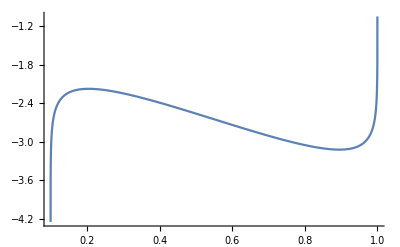

```mathematica
(*Plot to find the possible number of Einstein points*)
Plot[z[x,4,1,.1]-2*x,{x,.1,1}]
```

```mathematica
PhaseSpacexy=Manipulate[StreamPlot[{Eqx[q1,ℛ,cz],Eqy[q1,ℛ,cz]},{x,ℛ,1},{y,-1,1}],{q1,0.01,10,Appearance->"Open"},{ℛ,0,1,Appearance->"Open"},{cz,-5,5,Appearance->"Open"}]

Acc=Manipulate[ContourPlot[{2*x-z[x,q1,cz,ℛ]==0},{x,ℛ,1},{y,-1,1},ContourStyle->{Red, Thick}],{q1,0.01,10,Appearance->"Open"},{ℛ,0,1,Appearance->"Open"},{cz,-5,5,Appearance->"Open"}]

Show[PhaseSpacexy, Acc] //Dynamic
```

```mathematica
Integrate[1/(z[x,q1,cz,ℛ]*q1*(x-ℛ)*(1-x)),x]
```

(∫1/((1-x) (x-ℛ) (-cz-x+Log[(x-ℛ)/(1-x)]/(q1 (1-ℛ))))ⅆx)/q1